```mathematica
height=0.5*2;
ks=2*2*Pi/4*3/2;
hs=0.9*height;
M2=3;
g=980;
σ=72;
ρ=1;
```

## One dimensional sinusoidal heterogeneity

```mathematica
κ[kx_, n_]:=kx+n*ks;H1flat[kx_,A_]:=Table[(1/2-Tanh[Norm[κ[kx,n1]]*height]/2)*(g+σ/ρ*Norm[κ[kx,n1]]^2)*Norm[κ[kx,n1]]*(BesselI[n2-n1,-Norm[κ[kx,n1]]*A]-1/2*ks*A*(κ[kx,n1]/Norm[κ[kx,n1]]*(BesselI[n2-n1+1,-Norm[κ[kx,n1]]*A]-BesselI[n2-n1-1,-Norm[κ[kx,n1]]*A])))-(1/2+Tanh[Norm[κ[kx,n1]]*height]/2)*(g+σ/ρ*Norm[κ[kx,n1]]^2)*Norm[κ[kx,n1]]*(BesselI[n2-n1,Norm[κ[kx,n1]]*A]-1/2*ks*A*(κ[kx,n1]/Norm[κ[kx,n1]]*(BesselI[n2-n1+1,Norm[κ[kx,n1]]*A]-BesselI[n2-n1-1,Norm[κ[kx,n1]]*A]))),{n1,-M2,M2},{n2,-M2,M2}];
H2flat[kx_,A_]:=Table[(1/2-Tanh[Norm[κ[kx,n1]]*height]/2)*(BesselI[n2-n1,-Norm[κ[kx,n1]]*A]-1/2*ks*A*(κ[kx,n1]/Norm[κ[kx,n1]]*(BesselI[n2-n1+1,-Norm[κ[kx,n1]]*A]-BesselI[n2-n1-1,-Norm[κ[kx,n1]]*A])))+(1/2+Tanh[Norm[κ[kx,n1]]*height]/2)*(BesselI[n2-n1,Norm[κ[kx,n1]]*A]-1/2*ks*A*(κ[kx,n1]/Norm[κ[kx,n1]]*(BesselI[n2-n1+1,Norm[κ[kx,n1]]*A]-BesselI[n2-n1-1,Norm[κ[kx,n1]]*A]))),{n1,-M2,M2},{n2,-M2,M2}];
```

```mathematica
num=100;
sysflat[kx_,A_]:={H1flat[kx,A],H2flat[kx,A]}
AbsoluteTiming[vals0=Table[{kx,#^(1/2)/(2*Pi)}&/@SingularValueList[sysflat[kx,0.01]],{kx,0.01,ks,(ks/2-0.01)/num}];]
AbsoluteTiming[vals1=Table[{kx,#^(1/2)/(2*Pi)}&/@SingularValueList[sysflat[kx,hs]],{kx,0.01,ks,(ks/2-0.01)/num}];]
```

{2.33289,Null}

{2.80478,Null}

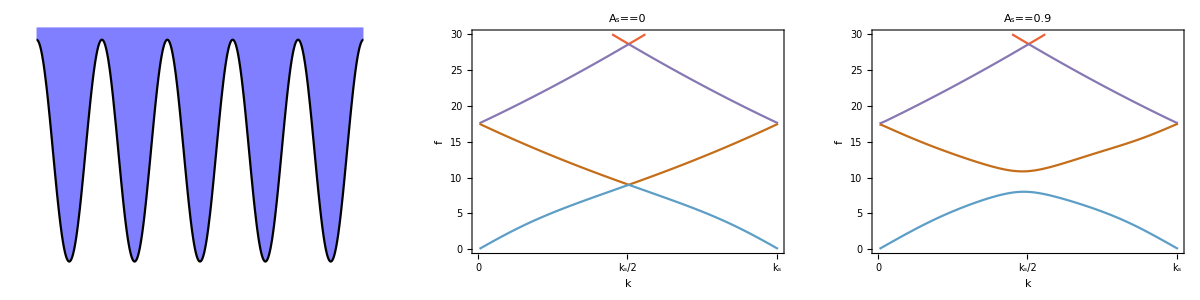

```mathematica
p=Grid[{{Plot[hs*Cos[ks*x],{x,0,2*Pi*5/ks},PlotStyle->Black,PlotRange->{-1.1*hs,height},Axes->False,Filling->Top,FillingStyle->Directive[Opacity[0.5],Blue],ImageSize->300],ListPlot[Transpose[vals0[[All,All,2]]],Joined->True,PlotRange->{0,30},Axes->False,Frame->True,FrameLabel->{k,f},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],FrameTicks->{{Automatic,Automatic},{{{0,0},{num,Subscript[k,s]/2},{2*num,Subscript[k,s]}},{{0,""},{num,""},{2*num,""}}}},ImageSize->300,PlotLabel->Subscript[A,s]==0,AspectRatio->1,ImagePadding->{{65,15},{65,15}}],
ListPlot[Transpose[vals1[[All,All,2]]],Joined->True,PlotRange->{0,30},Axes->False,Frame->True,FrameLabel->{k,f},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],FrameTicks->{{Automatic,Automatic},{{{0,0},{num,Subscript[k,s]/2},{2*num,Subscript[k,s]}},{{0,""},{num,""},{2*num,""}}}},ImageSize->300,PlotLabel->Subscript[A,s]==hs,AspectRatio->1,ImagePadding->{{65,15},{65,15}}]}}]
```

```mathematica
Differences[vals1[[100]]][[-1,2]]
```

-2.87676

## Square heterogeneity

```mathematica
κ[kx_,ky_, n_,m_]:={kx+n*ks,ky+m*ks};
H1square[kx_,ky_,A_]:=ArrayFlatten[-Table[(1/2-Tanh[Norm[κ[kx,ky,n1,m1]]*height]/2)*(g+σ/ρ*Norm[κ[kx,ky,n1,m1]]^2)*Norm[κ[kx,ky,n1,m1]]*(BesselI[n1-n2,Norm[κ[kx,ky,n1,m1]]*A/2]*BesselI[m1-m2,Norm[κ[kx,ky,n1,m1]]*A/2]-1/4*ks*A*(κ[kx,ky,n1,m1].{1,0}/Norm[κ[kx,ky,n1,m1]](BesselI[n1-n2+1,Norm[κ[kx,ky,n1,m1]]*A/2]-BesselI[n1-n2-1,Norm[κ[kx,ky,n1,m1]]*A/2])*BesselI[m1-m2,Norm[κ[kx,ky,n1,m1]]*A/2]+κ[kx,ky,n1,m1].{0,1}/Norm[κ[kx,ky,n1,m1]]*BesselI[n1-n2,Norm[κ[kx,ky,n1,m1]]*A/2]*(BesselI[m1-m2+1,Norm[κ[kx,ky,n1,m1]]*A/2]-BesselI[m1-m2-1,Norm[κ[kx,ky,n1,m1]]*A/2])))-(1/2+Tanh[Norm[κ[kx,ky,n1,m1]]*height]/2)*(g+σ/ρ*Norm[κ[kx,ky,n1,m1]]^2)*Norm[κ[kx,ky,n1,m1]]*(BesselI[n1-n2,-Norm[κ[kx,ky,n1,m1]]*A/2]*BesselI[m1-m2,-Norm[κ[kx,ky,n1,m1]]*A/2]-1/4*ks*A*(κ[kx,ky,n1,m1].{1,0}/Norm[κ[kx,ky,n1,m1]](BesselI[n1-n2+1,-Norm[κ[kx,ky,n1,m1]]*A/2]-BesselI[n1-n2-1,-Norm[κ[kx,ky,n1,m1]]*A/2])*BesselI[m1-m2,-Norm[κ[kx,ky,n1,m1]]*A/2]+κ[kx,ky,n1,m1].{0,1}/Norm[κ[kx,ky,n1,m1]]*BesselI[n1-n2,-Norm[κ[kx,ky,n1,m1]]*A/2]*(BesselI[m1-m2+1,-Norm[κ[kx,ky,n1,m1]]*A/2]-BesselI[m1-m2-1,-Norm[κ[kx,ky,n1,m1]]*A/2]))),{n1,-M2,M2},{n2,-M2,M2},{m1,-M2,M2},{m2,-M2,M2}]];
H2square[kx_,ky_,A_]:=ArrayFlatten[-Table[(1/2-Tanh[Norm[κ[kx,ky,n1,m1]]*height]/2)*(BesselI[n1-n2,Norm[κ[kx,ky,n1,m1]]*A/2]*BesselI[m1-m2,Norm[κ[kx,ky,n1,m1]]*A/2]-1/4*ks*A*(κ[kx,ky,n1,m1].{1,0}/Norm[κ[kx,ky,n1,m1]](BesselI[n1-n2+1,Norm[κ[kx,ky,n1,m1]]*A/2]-BesselI[n1-n2-1,Norm[κ[kx,ky,n1,m1]]*A/2])*BesselI[m1-m2,Norm[κ[kx,ky,n1,m1]]*A/2]+κ[kx,ky,n1,m1].{0,1}/Norm[κ[kx,ky,n1,m1]]*BesselI[n1-n2,Norm[κ[kx,ky,n1,m1]]*A/2]*(BesselI[m1-m2+1,Norm[κ[kx,ky,n1,m1]]*A/2]-BesselI[m1-m2-1,Norm[κ[kx,ky,n1,m1]]*A/2])))+(1/2+Tanh[Norm[κ[kx,ky,n1,m1]]*height]/2)*(BesselI[n1-n2,-Norm[κ[kx,ky,n1,m1]]*A/2]*BesselI[m1-m2,-Norm[κ[kx,ky,n1,m1]]*A/2]-1/4*ks*A*(κ[kx,ky,n1,m1].{1,0}/Norm[κ[kx,ky,n1,m1]](BesselI[n1-n2+1,-Norm[κ[kx,ky,n1,m1]]*A/2]-BesselI[n1-n2-1,-Norm[κ[kx,ky,n1,m1]]*A/2])*BesselI[m1-m2,-Norm[κ[kx,ky,n1,m1]]*A/2]+κ[kx,ky,n1,m1].{0,1}/Norm[κ[kx,ky,n1,m1]]*BesselI[n1-n2,-Norm[κ[kx,ky,n1,m1]]*A/2]*(BesselI[m1-m2+1,-Norm[κ[kx,ky,n1,m1]]*A/2]-BesselI[m1-m2-1,-Norm[κ[kx,ky,n1,m1]]*A/2]))),{n1,-M2,M2},{n2,-M2,M2},{m1,-M2,M2},{m2,-M2,M2}]];
```

```mathematica
num=25;
syssquare[kx_,ky_,A_]:={H1square[kx,ky,A],H2square[kx,ky,A]}
AbsoluteTiming[vals1=Table[{kx,#^(1/2)/(2*Pi)}&/@SingularValueList[syssquare[kx,0,hs]],{kx,0.01,ks/2,(ks/2-0.01)/num}];]
AbsoluteTiming[vals2=Table[{ky,#^(1/2)/(2*Pi)}&/@SingularValueList[syssquare[ks/2,ky,hs]],{ky,0.01,ks/2,(ks/2-0.01)/num}];]
AbsoluteTiming[vals3=Table[{2^(1/2)*k,#^(1/2)/(2*Pi)}&/@SingularValueList[syssquare[k,k,hs]],{k,0.01,ks/2,(ks/2-0.01)/num}];]
AbsoluteTiming[vals4=Table[{kx,#^(1/2)/(2*Pi)}&/@SingularValueList[syssquare[kx,0,0.01]],{kx,0.01,ks/2,(ks/2-0.01)/num}];]
AbsoluteTiming[vals5=Table[{ky,#^(1/2)/(2*Pi)}&/@SingularValueList[syssquare[ks/2,ky,0.01]],{ky,0.01,ks/2,(ks/2-0.01)/num}];]
AbsoluteTiming[vals6=Table[{2^(1/2)*k,#^(1/2)/(2*Pi)}&/@SingularValueList[syssquare[k,k,0.01]],{k,0.01,ks/2,(ks/2-0.01)/num}];]
```

{53.176,Null}

{57.3164,Null}

{52.448,Null}

{48.8373,Null}

{52.8062,Null}

{47.8361,Null}

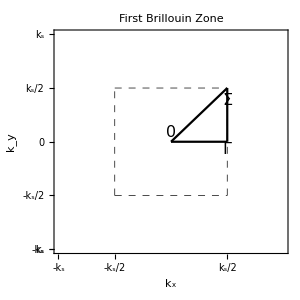
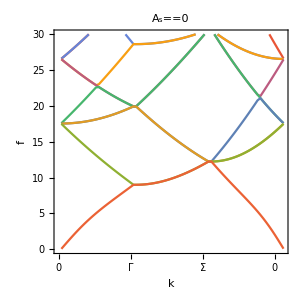
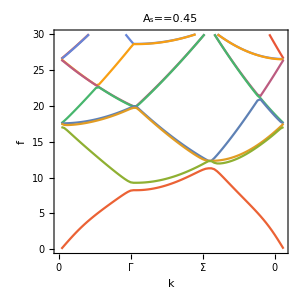
-Graphics3D- | -Graphics- | -Graphics- | -Graphics-

```mathematica
p=Grid[{{ListPlot3D[Flatten[Table[{x,y,1/2*(hs*Sin[ks*x]+hs*Sin[ks*y])},{x,0,2*Pi*5/ks,2*Pi*5/ks/100},{y,0,2*Pi*5/ks,2*Pi*5/ks/100}],1],PlotRange->{-hs,height},Boxed->False,Axes->False,Filling->Top,FillingStyle->Directive[Opacity[0.5],Blue],ImageSize->300],Show[ParametricPlot[{{k,-ks/2},{k,ks/2},{-ks/2,k},{ks/2,k}},{k,-ks/2,ks/2},PlotStyle->Directive[Black,Dashed,AbsoluteThickness[0.5]],Axes->False,Frame->True,FrameLabel->{Subscript[k,x],Subscript[k,y]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],PlotRange->{{-ks,ks},{-ks,ks}},ImageSize->300,FrameTicks->{{{{-ks,Subscript[k,s]},{-ks,-Subscript[k,s]},{-ks/2,-Subscript[k,s]/2},{0,0},{ks/2,Subscript[k,s]/2},{ks,Subscript[k,s]}},{{-ks,""},{-ks,""},{-ks/2,""},{0,""},{ks/2,""},{ks,""}}},{{{-ks,-Subscript[k,s]},{-ks,-Subscript[k,s]},{-ks/2,-Subscript[k,s]/2},{0,0},{ks/2,Subscript[k,s]/2},{ks,Subscript[k,s]}},{{-ks,""},{-ks,""},{-ks/2,""},{0,""},{ks/2,""},{ks,""}}}},ImagePadding->{{65,15},{65,15}},PlotLabel->"First Brillouin Zone"],ParametricPlot[{{k,0},{ks/2,k},{ks/2-k,ks/2-k}},{k,0,ks/2},PlotStyle->Directive[Black],Axes->False,Frame->True,FrameLabel->{Subscript[k,x],Subscript[k,y]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],PlotRange->{{-ks,ks},{-ks,ks}},PlotLabels->Placed[{0,Γ,Σ},Scaled[0]]]],ListPlot[Transpose[Join[vals4[[All,All,2]],vals5[[All,All,2]],Reverse[vals6[[All,All,2]]]]],PlotLabel->Subscript[A,s]==0,Joined->True,PlotRange->{0,30},Axes->False,Frame->True,FrameLabel->{k,f},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],FrameTicks->{{Automatic,Automatic},{{{0,0},{num,"Γ"},{2*num,"Σ"},{3*num,0}},{{0,""},{num,""},{2*num,""},{3*num,""}}}},ImageSize->300,AspectRatio->1,ImagePadding->{{65,15},{65,15}}],
ListPlot[Transpose[Join[vals1[[All,All,2]],vals2[[All,All,2]],Reverse[vals3[[All,All,2]]]]],PlotLabel->Subscript[A,s]==0.45,Joined->True,PlotRange->{0,30},Axes->False,Frame->True,FrameLabel->{k,f},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],FrameTicks->{{Automatic,Automatic},{{{0,0},{num,"Γ"},{2*num,"Σ"},{3*num,0}},{{0,""},{num,""},{2*num,""},{3*num,""}}}},ImageSize->300,AspectRatio->1,ImagePadding->{{65,15},{65,15}}]}}]
```

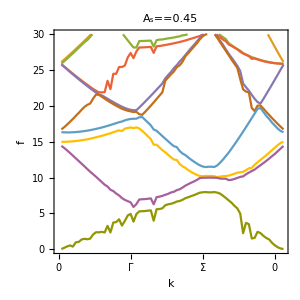

```mathematica
ListPlot[Transpose[Join[vals1[[All,-10;;-1,2]],vals2[[All,-10;;-1,2]],Reverse[vals3[[All,-10;;-1,2]]]]],PlotLabel->Subscript[A,s]==0.45,Joined->True,PlotRange->{0,30},Axes->False,Frame->True,FrameLabel->{k,f},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],FrameTicks->{{Automatic,Automatic},{{{0,0},{num,"Γ"},{2*num,"Σ"},{3*num,0}},{{0,""},{num,""},{2*num,""},{3*num,""}}}},ImageSize->300,AspectRatio->1,ImagePadding->{{65,15},{65,15}}]
```